```mathematica
?ContourPlot
```

RowBox[{"ContourPlot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a contour plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] and StyleBox["y", "TI"]. 
RowBox[{"ContourPlot", "[", RowBox[{RowBox[{StyleBox["f", "TI"], "==", StyleBox["g", "TI"]}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots contour lines for which RowBox[{StyleBox["f", "TI"], "=", StyleBox["g", "TI"]}]. 
RowBox[{"ContourPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], "==", SubscriptBox[StyleBox["g", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], "==", SubscriptBox[StyleBox["g", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several contour lines.

```mathematica
ContourPlot[y^2+3x y- y==x^3-3x^2+x+1,{x,-2,7},{y,-3,3},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},AxesLabel->{,Style["    ";y^2 +3x y- y==x^3-3x^2+x+1,Orange,30]},Background->LightBrown,ImageSize-> 1000]
```

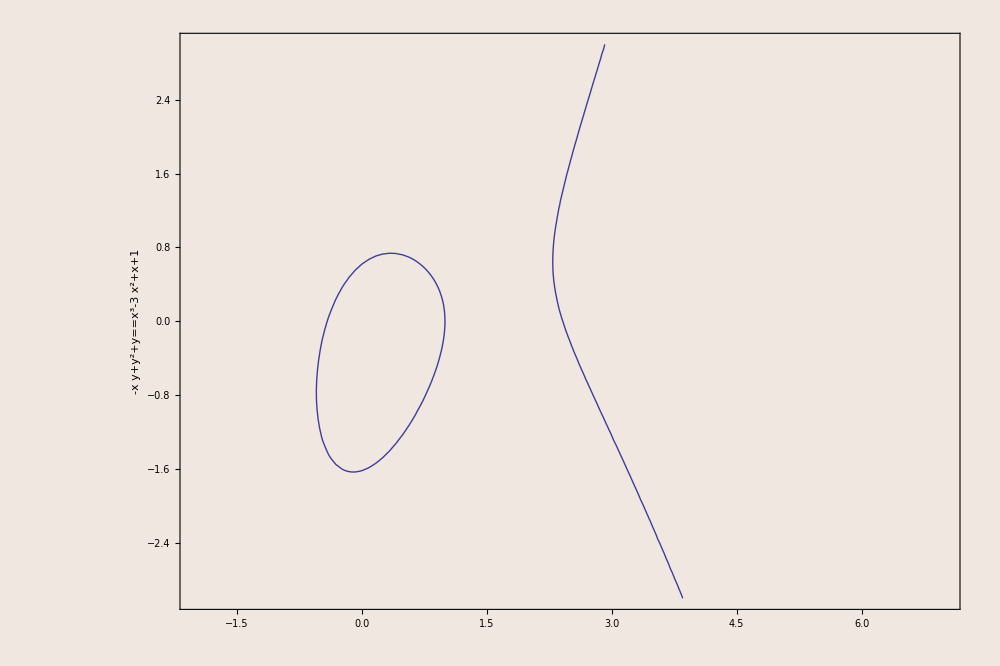

```mathematica
Framed[ContourPlot[y^2-x y+ y==x^3-3x^2+x+1,{x,-2,7},{y,-3,3},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},AxesLabel->{,Style[y^2 -x y+ y==x^3-3x^2+x+1,Orange,30]},Background->LightBrown,ImageSize-> 1000],FrameStyle-> Thick]
```

```mathematica
Framed[ContourPlot[y^2-2x y==x^3-x^2,{x,-2,7},{y,-3,3},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},AxesLabel->{,Style["SINGULAR",Red,30]},Background-> LightBrown,ImageSize-> 1000],FrameStyle-> Thick]
```

```mathematica
Framed[ContourPlot[y^2+x y+y==x^3+x^2+x+1,{x,-2,7},{y,-3,3},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},AxesLabel->{,Style[y^2+x y+y==x^3+x^2+x+1,Orange,30]},Background-> LightBrown,ImageSize-> 1000],FrameStyle-> Thick]
```

```mathematica
Framed[ContourPlot[y^2-x y+y==x^3+x^2-x-1,{x,-2,7},{y,-3,3},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},AxesLabel->{,Style[y^2-x y+y==x^3+x^2-x-1,Orange,30]},Background-> LightBrown,ImageSize-> 1000],FrameStyle-> Thick]
```

```mathematica
Framed[ContourPlot[y^2==x^3+x^2-x,{x,-2,7},{y,-3,3},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},AxesLabel->{,Style[y^2==x^3+x^2-x,Orange,30]},Background-> LightBrown,ImageSize-> 1000],FrameStyle-> Thick]
```

```mathematica
Framed[ContourPlot[y^2==x^3+x^2,{x,-2,7},{y,-3,3},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},AxesLabel->{,Style["SINGULAR",Red,30]},Background-> LightBrown,ImageSize-> 1000],FrameStyle-> Thick]
```

```mathematica
Simplify[ReplaceAll[{y^2+a1 x y+a3 y - x^3 -a2 x^2 - a4 x - a6},{y-> y-(a1 x + a3)/2}]]
```

{1/4 (-a3^2-4 a6-2 a1 a3 x-4 a4 x-a1^2 x^2-4 a2 x^2-4 x^3+4 y^2)}

```mathematica
Simplify[ReplaceAll[{y^2- x^3 -a2 x^2 - a4 x - a6},{x-> x-a2/3}]]
```

{-(2 a2^3)/27+(a2 a4)/3-a6+(a2^2 x)/3-a4 x-x^3+y^2}

```mathematica
Simplify[ReplaceAll[y^2(1-x^2)==(1+3x^2),{x-> (x-2)/x,y-> y/((x-1))}]]
```

(4 y^2)/((-1+x) x^2)==1+(3 (-2+x)^2)/x^2

```mathematica
y^2==Expand[(x^2+3 (-2+x)^2)(x-1)/4]
```

y^2==-3+6 x-4 x^2+x^3

```mathematica
ContourPlot[{y^2(1-x^2)==(1+3x^2),x^2/4+y^2/16==1},{x,-3,3},{y,-5,5},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},AxesLabel->{,Style[y^2(1-x^2)==(1+3x^2),10]},Background-> LightBrown,ImageSize-> 300]
```

```mathematica
Framed[ContourPlot[(x^2+y^2)^2==2(x^2-y^2),{x,-1.5,1.5},{y,-.75,.75},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},Background-> LightBrown,ImageSize-> 1000],FrameStyle-> Thick]
```

```mathematica
Framed[ContourPlot[(x^2/4+y^2/16)==1,{x,-2,2},{y,-4,4},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},Background-> LightBrown,ImageSize-> 1000],FrameStyle-> Thick]
```

```mathematica
Simplify[Integrate[a^2/Sqrt[a^4-r^4],{r,0,a}]]
```

ConditionalExpression[(a √π Gamma[5/4])/Gamma[3/4],a>0]

```mathematica
Simplify[Integrate[Sqrt[(1+3r^2)/(1-r^2)],{r,0,1}]]
```

EllipticE[-3]

```mathematica
ContourPlot[{y^2-x y+ y==x^3-3x^2+x+1},{x,-2,4},{y,-3,3},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},AxesLabel->{,Style[y^2 -x y+ y==x^3-3x^2+x+1,30]},Background->LightBrown,ImageSize-> 700,PerformanceGoal->"Quality",PlotPoints->{15,20}]
```

```mathematica
ContourPlot[{y^2-x y+ y==x^3-3x^2+x+1},{x,-2,4},{y,-3,3},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},AxesLabel->{,Style[y^2 -x y+ y==x^3-3x^2+x+1,30]},Background->LightBrown,ImageSize-> 700,PerformanceGoal->"Quality",PlotPoints->{15,20}]
```

```mathematica
ContourPlot[{y^2-x y+ y==x^3-3x^2+x+1},{x,-2,4},{y,-3,3},AspectRatio -> Automatic,Axes->True ,Frame-> True,AxesOrigin->{0,0},AxesLabel->{,Style[y^2 -x y+ y==x^3-3x^2+x+1,30]},Background->LightBrown,ImageSize-> 700,PerformanceGoal->"Quality",PlotPoints->{15,20}]
```

```mathematica
EcAdd[{a_,b_},p1_,p2_]:=Module[{m,x1,y1,x2,y2,x3,y3,w},{x1,y1}=p1;{x2,y2}=p2;
(*Handle identity cases*)If[x1==∞,Return[p2]];
(*Subscript[p,1]+(-Subscript[p,1])=∞*)If[x1==x2&&y1+y2==0,Return[{∞,∞}]];
(*If we are doubling a point*)If[p1==p2,(*Check for vertical tangent*)If[y1==0,Return[{∞,∞}]];
(*Compute the slope of the tangent*)m=(3 x1^2+a)/(2 y1);,(*else compute the slope of the chord*)m=(y2-y1)/(x2-x1)];
x3=m^2-x1-x2;
y3=m (x1-x3)-y1;
{x3,y3}];

EcY[{a_,b_},x_]:=Sqrt[x^3+a x+b];

PlotEcAdd[pt1_,pt2_]:=Module[{pt3,pt4},pt4=EcAdd[{a,b},pt1,pt2];
pt3={pt4[[1]],-pt4[[2]]};
{ContourPlot[y^2==x^3+a x+b,{x,-5,5},{y,-4,4},Axes->True,PerformanceGoal->"Quality",PlotPoints->{15,20}],Graphics[{PointSize[0.02],Point[{pt1,pt2,pt3}],ColorData[1,2],Point[pt4],Line[{pt1,pt3}],ColorData[1,3],Line[{pt3,pt4}]}]
}];

a=-5;b=-1;x1=-1.2;pt1={x1,EcY[{a,b},x1]};Print[pt1]

DemoEcAdd[]:=Manipulate[Show[PlotEcAdd[pt1,{pt[[1]],EcY[{a,b},pt[[1]]]}],ImageSize->440],Style[Row[{" Elliptic Curve Point Addition ",TraditionalForm[y^2==x^3+a x+b]}],18],{pt,{-1.2,0},{-0.38,0},Locator,Appearance->Style["|",20,Red]}]
```

{-1.2,1.80887}

```mathematica
Manipulate[Show[PlotEcAdd[pt1,{pt[[1]],EcY[{a,b},pt[[1]]]}],ImageSize->600,PlotLabel->Style[Row[{TraditionalForm[y^2==x^3+a x+b]}],18]],{pt,{-1.2,0},{-0.38,0},Locator,Appearance->Style["|",20,Red]},SaveDefinitions->True]
```